```mathematica
randomExample[n_]:=Module[{r,p,g,i},
Table[
r=RandomInteger[];
p=If[r===0,Disk[RandomReal[{-1,1},2],.5],(pt=RandomReal[{-1,1},2];Rectangle[pt-.5,pt+.5])];
g=Graphics[p,PlotRange->1,Background->LightBlue];
i=Image[g,ImageSize->{100,100}];
i->If[r===0,"Disk","Rectangle"],
n]]
```

```mathematica
randomExample[6]
```

{-Graphics-→Rectangle,-Graphics-→Disk,-Graphics-→Disk,-Graphics-→Disk,-Graphics-→Disk,-Graphics-→Disk}

```mathematica
training=randomExample[2000];
```

```mathematica
RandomSample[training,5]
```

{-Graphics-→Disk,-Graphics-→Disk,-Graphics-→Rectangle,-Graphics-→Disk,-Graphics-→Rectangle}

```mathematica
net=NetGraph[{
ConvolutionLayer[6,{3,3}],
ElementwiseLayer[Ramp],
PoolingLayer[{3,3},"Stride"->2],
FlattenLayer[],
DotPlusLayer[50],
ElementwiseLayer[Ramp],
DotPlusLayer[2],
SoftmaxLayer[]
},
{1->2->3->4->5->6->7->8},
"Input"->NetEncoder[{"Image",{100,100}}],
"Output"->NetDecoder[{"Class",{"Disk","Rectangle"}}]
]
```

NetGraph[]

```mathematica
net=NetInitialize[net];
result=NetTrain[net,training,TargetDevice->"GPU"]
```

NetGraph[]

```mathematica
Dataset[Table[<|"image"->First[v],"actual"->Last[v],"predicted"->result[First[v]]|>,{v,randomExample[5]}]]
```

Dataset[<>]

```mathematica
validation=randomExample[100];
```

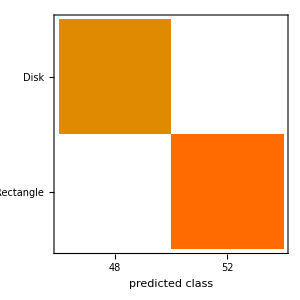

```mathematica
cm=ClassifierMeasurements[result,validation];
cm["ConfusionMatrixPlot"]
```

```mathematica
layer=NetExtract[result,1]
```

None

```mathematica
Image/@layer[NetEncoder[{"Image",{100,100}}][randomExample[1][[1,1]]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
rr=Take[result,{1,8}]
```

NetGraph[]

```mathematica
randomExample[1]
```

{-Graphics-→Rectangle}

```mathematica
i=CurrentImage[]
```

-Graphics-

```mathematica
ImageDimensions[i]
```

{320,240}

```mathematica
320-240
```

80

```mathematica
i2=ImageResize[ImageTake[i,{1,240},{40,280}],{100,100}]
```

-Graphics-

```mathematica
ImageResize[i,{100,100}]
```

-Graphics-

```mathematica
i2
```

-Graphics-

```mathematica
result[i2,"Probabilities"]
```

<|Disk→0.999787,Rectangle→0.000213193|>

```mathematica
rr[randomExample[1][[1,1]]]
```

```mathematica
SoftmaxLayer[][{-5.3758111000061035,-0.4291389286518097}]
```

{0.00705687,0.992943}

```mathematica
Table[{i=randomExample[1][[1,1]],Image/@layer[NetEncoder[{"Image",{100,100}}][i]]},10]//Grid
```

-Graphics- | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics- | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics- | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics- | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics- | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics- | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics- | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics- | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics- | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
-Graphics- | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}